```mathematica
Flatten[DSolve[{x'[t]==(mu*x[t])/Exp[t*(1-α)],x[0]==x0},x[t], t]]
```

{x[t]→ⅇ^(-mu/(-1+α)+(ⅇ^(t (-1+α)) mu)/(-1+α)) x0}

```mathematica
Flatten[Assuming[α==1,DSolve[{x'[t]==(mu*x[t])/Exp[t*(1-α)],x[0]==x0},x[t], t]]]
```

{x[t]→ⅇ^(mu t) x0}

```mathematica
ClearAll[x0,mu, α]
x0 = 1;
mu = 1;
(*α = 0.5;*)
(*Manipulate[Plot[DSolve[{x'[t]==(mu*x[t])/Exp[t*(1-α)],x[0]==x0},x[t], t][[1,1,2]]/.t->τ, {τ,0, 5}, PlotRange->{{0, 5},{0, 100}}], {{α, 1/2},0, 1}]*)
```

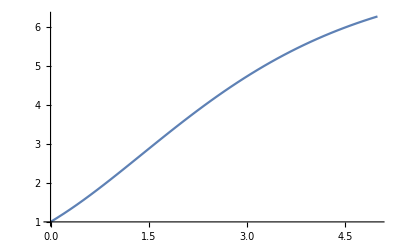

```mathematica
ClearAll[x0,mu, α]
x0 = 1;
mu = 1;
α = 0.5;
s=NDSolve[{x'[t]==(mu*x[t])/Exp[t*(1-α)],x[0]==x0},x[t], {t,0, 5}];
Plot[Evaluate[x[t]/.s],{t,0,5},PlotRange->All]
```